# Automatic congruences for diagonals of rational functions

## computation notebook

Eric Rowland
http://people.hofstra.edu/Eric_Rowland/papers.html#Automatic_congruences_for_diagonals_of_rational_functions

## Introduction

This notebook contains the computations performed in the paper “Automatic congruences for diagonals of rational functions” by Eric Rowland and Reem Yassawi.

To re-run the computations, first you will need to load the IntegerSequences package.  You can load it directly from the web by evaluating the following cell.

```mathematica
Import["http://people.hofstra.edu/Eric_Rowland/packages/IntegerSequences.m"]
```

You can also download it from http://people.hofstra.edu/Eric_Rowland/packages.html#IntegerSequences and then evaluate the following.  (If you need help, see loading a package.)

```mathematica
<<IntegerSequences`
```

To check that it loaded correctly, re-evaluate the following.

```mathematica
MotzkinNumber[10]
```

2188

## Computing automata for algebraic sequences modulo p^α

This function determines which residues modulo a prime power are never output by a finite automaton when fed the base-p digits of an integer:

```mathematica
MissingResidues[sequence:_AutomaticSequence[_],modulus_Integer]:=
With[{automaton=AutomaticSequenceAutomaton[sequence]},
Complement[Range[0,modulus-1],Replace[Cases[First[automaton],{_->state_,Except[0]}:>state],AutomatonOutputRules[automaton],{1}]]
]
```

### version note

The computations in the paper were carried out for algebraic sequences with initial term 0.  For example:

```mathematica
Table[AlgebraicSequence[Function[y,-y+x (1+y)^2],x][n],{n,0,10}]
```

{0,1,2,5,14,42,132,429,1430,4862,16796}

```mathematica
AutomatonGraph[AutomaticSequenceAutomaton[AutomaticSequenceReduce[Mod[AlgebraicSequence[Function[y,-y+x (1+y)^2],x][n],2],n,Method->"Diagonal",Minimize->False]],GraphLayout->"SpringEmbedding"]
```

-Graphics-

The code now supports general algebraic sequences, in which the initial term is not required to be 0.  Such a sequence is specified using SeriesRoot.
(Additionally, the automaton is now minimized by default.)

```mathematica
AutomatonGraph[AutomaticSequenceAutomaton[AutomaticSequenceReduce[Mod[AlgebraicSequence[SeriesRoot[{Function[y,-y+1+x y^2],1+O[x]^1}]][n],2],n,Method->"Diagonal"]]]
```

-Graphics-

Direct use of CatalanNumber is also supported.

```mathematica
AutomatonGraph[AutomaticSequenceAutomaton[AutomaticSequenceReduce[Mod[CatalanNumber[n],2],n]]]
```

-Graphics-

However, to maintain consistency with the published paper, the sequences in this section have initial term 0, and the automata are not minimized.

### Catalan numbers (A000108)

```mathematica
Table[CatalanNumber[n],{n,0,10}]
```

{1,1,2,5,14,42,132,429,1430,4862,16796}

```mathematica
Series[(1-√(1-4 x))/(2 x),{x,0,10}]
```

1+x+2 x^2+5 x^3+14 x^4+42 x^5+132 x^6+429 x^7+1430 x^8+4862 x^9+16796 x^10+O[x]^11

Remove the constant term:

```mathematica
-y+1+x y^2/.y->y+1
```

-y+x (1+y)^2

#### 2^α

```mathematica
With[{sequence=AutomaticSequenceReduce[Mod[AlgebraicSequence[Function[y,-y+x (1+y)^2],x][n],2],n,Method->"Diagonal",Minimize->False]},AutomatonGraph[AutomaticSequenceAutomaton[sequence],GraphLayout->"SpringEmbedding"]]
```

-Graphics-

```mathematica
With[{sequence=AutomaticSequenceReduce[Mod[AlgebraicSequence[Function[y,-y+x (1+y)^2],x][n],2^2],n,Method->"Diagonal",Minimize->False]},AutomatonGraph[AutomaticSequenceAutomaton[sequence],GraphLayout->"SpringEmbedding"]]
```

-Graphics-

```mathematica
With[{sequence=AutomaticSequenceReduce[Mod[AlgebraicSequence[Function[y,-y+x (1+y)^2],x][n],2^3],n,Method->"Diagonal",Minimize->False]},AutomatonGraph[AutomaticSequenceAutomaton[sequence],GraphLayout->"SpringEmbedding",VertexSize->.3]]
```

-Graphics-

```mathematica
Column[AbsoluteTiming[Grid[Function[modulus,{modulus,MissingResidues[AutomaticSequenceReduce[Mod[AlgebraicSequence[Function[y,-y+x (1+y)^2],x][n],modulus],n,Method->"Diagonal",Minimize->False],modulus]}]/@(2^Range[6])]]]
```

8.68214
2 | {}
4 | {3}
8 | {3,7}
16 | {3,7,9,11,15}
32 | {3,7,9,11,15,17,19,21,23,25,26,27,31}
64 | {3,7,9,10,11,13,15,17,19,21,23,25,26,27,31,33,35,37,39,41,43,47,49,51,53,55,57,58,59,63}

```mathematica
AbsoluteTiming[With[{modulus=2^7},MissingResidues[AutomaticSequenceReduce[Mod[AlgebraicSequence[Function[y,-y+x (1+y)^2],x][n],modulus],n,Method->"Diagonal",Minimize->False,Monitor->True],modulus]]]
```

{79.1532,{3,7,9,10,11,13,15,17,18,19,21,23,25,26,27,31,33,35,37,39,41,43,47,49,51,53,54,55,57,58,59,61,63,65,66,67,69,71,73,74,75,77,79,81,83,85,87,89,90,91,95,97,98,99,101,103,105,106,107,109,111,113,115,117,119,121,122,123,127}}

```mathematica
AbsoluteTiming[With[{modulus=2^8},MissingResidues[AutomaticSequenceReduce[Mod[AlgebraicSequence[Function[y,-y+x (1+y)^2],x][n],modulus],n,Method->"Diagonal",Minimize->False,Monitor->True],modulus]]]
```

{773.626,{3,7,9,10,11,13,15,17,18,19,21,22,23,25,26,27,31,33,34,35,37,39,41,43,45,47,49,51,53,54,55,57,58,59,61,62,63,65,66,67,69,71,73,74,75,77,79,81,82,83,85,86,87,89,90,91,95,97,98,99,101,103,105,106,107,109,111,113,115,117,118,119,121,122,123,127,129,130,131,133,135,137,138,139,141,143,145,146,147,149,151,153,154,155,157,159,161,163,165,167,169,170,171,175,177,178,179,181,182,183,185,186,187,189,191,193,194,195,197,199,201,202,203,205,207,209,211,213,215,217,218,219,223,225,226,227,229,231,233,234,235,237,239,241,243,245,247,249,250,251,253,255}}

```mathematica
AbsoluteTiming[With[{modulus=2^9},MissingResidues[AutomaticSequenceReduce[Mod[AlgebraicSequence[Function[y,-y+x (1+y)^2],x][n],modulus],n,Method->"Diagonal",Minimize->False,Monitor->True],modulus]]]
```

{9400.56,{3,6,7,9,10,11,13,15,17,18,19,21,22,23,25,26,27,31,33,34,35,37,39,41,43,45,47,49,50,51,53,54,55,57,58,59,61,62,63,65,66,67,69,71,73,74,75,77,79,81,82,83,85,86,87,89,90,91,93,95,97,98,99,101,103,105,106,107,109,111,113,115,117,118,119,121,122,123,127,129,130,131,133,134,135,137,138,139,141,142,143,145,146,147,149,150,151,153,154,155,157,159,161,162,163,165,167,169,170,171,173,175,177,178,179,181,182,183,185,186,187,189,191,193,194,195,197,199,201,202,203,205,207,209,210,211,213,214,215,217,218,219,220,223,225,226,227,229,230,231,233,234,235,237,239,241,242,243,245,247,249,250,251,253,255,257,258,259,261,263,265,266,267,269,270,271,273,274,275,277,278,279,281,282,283,285,287,289,290,291,293,294,295,297,298,299,301,303,305,307,309,310,311,313,314,315,317,318,319,321,322,323,325,327,329,330,331,333,335,337,338,339,341,342,343,345,346,347,348,351,353,354,355,357,359,361,362,363,365,367,369,371,373,374,375,377,378,379,381,382,383,385,386,387,389,391,393,394,395,397,399,401,402,403,405,407,409,410,411,413,415,417,419,421,422,423,425,426,427,431,433,434,435,437,438,439,441,442,443,445,446,447,449,450,451,453,455,457,458,459,461,463,465,467,469,471,473,474,475,478,479,481,482,483,485,487,489,490,491,493,495,497,499,501,502,503,505,506,507,509,510,511}}

#### 3 and 5

```mathematica
With[{sequence=AutomaticSequenceReduce[Mod[AlgebraicSequence[Function[y,-y+x (1+y)^2],x][n],3],n,Method->"Diagonal",Minimize->False]},AutomatonGraph[AutomaticSequenceAutomaton[sequence],GraphLayout->"SpringEmbedding"]]
```

-Graphics-

```mathematica
With[{sequence=AutomaticSequenceReduce[Mod[AlgebraicSequence[Function[y,-y+x (1+y)^2],x][n],5],n,Method->"Diagonal",Minimize->False]},AutomatonGraph[AutomaticSequenceAutomaton[sequence],GraphLayout->"SpringEmbedding"]]
```

-Graphics-

### Motzkin numbers (A001006)

```mathematica
Table[MotzkinNumber[n],{n,0,10}]
```

{1,1,2,4,9,21,51,127,323,835,2188}

```mathematica
Series[(1-x-√(1-2 x-3 x^2))/(2 x^2),{x,0,10}]
```

1+x+2 x^2+4 x^3+9 x^4+21 x^5+51 x^6+127 x^7+323 x^8+835 x^9+2188 x^10+O[x]^11

Remove the constant term:

```mathematica
x^2 y^2+(x-1) y+1/.y->y+1
```

1+(-1+x) (1+y)+x^2 (1+y)^2

```mathematica
With[{sequence=AutomaticSequenceReduce[Mod[AlgebraicSequence[Function[y,1+(-1+x) (1+y)+x^2 (1+y)^2],x][n],8],n,Method->{"Diagonal","Degree"->"High"},Minimize->False]},AutomatonGraph[AutomaticSequenceAutomaton[sequence],GraphLayout->"SpringEmbedding",ImageSize->500,VertexSize->.5]]
```

-Graphics-

```mathematica
With[{modulus=2^3},MissingResidues[AutomaticSequenceReduce[Mod[AlgebraicSequence[Function[y,x^2 y^2+(2 x^2+x-1) y+(x^2+x)],x][n],modulus],n,Method->"Diagonal",Minimize->False],modulus]]
```

{0}

```mathematica
AbsoluteTiming[With[{modulus=5^2},MissingResidues[AutomaticSequenceReduce[Mod[AlgebraicSequence[Function[y,x^2 y^2+(2 x^2+x-1) y+(x^2+x)],x][n],modulus],n,Method->"Diagonal",Minimize->False],modulus]]]
```

{0.973959,{0}}

```mathematica
AbsoluteTiming[With[{modulus=13^2},MissingResidues[AutomaticSequenceReduce[Mod[AlgebraicSequence[Function[y,x^2 y^2+(2 x^2+x-1) y+(x^2+x)],x][n],modulus],n,Method->"Diagonal",Minimize->False,Monitor->True],modulus]]]
```

{364.056,{0}}

### Riordan numbers (A005043)

```mathematica
Series[(1+x-√(1-2 x-3 x^2))/(2 (x+x^2)),{x,0,10}]
```

1+x^2+x^3+3 x^4+6 x^5+15 x^6+36 x^7+91 x^8+232 x^9+603 x^10+O[x]^11

```mathematica
1+(-1-x) y+x (1+x) y^2/.y->y+1
```

1+(-1-x) (1+y)+x (1+x) (1+y)^2

```mathematica
With[{modulus=3},MissingResidues[AutomaticSequenceReduce[Mod[AlgebraicSequence[Function[y,1+(-1-x) (1+y)+x (1+x) (1+y)^2],x][n],modulus],n,Method->"Diagonal",Minimize->False],modulus]]
```

{2}

```mathematica
With[{modulus=32},MissingResidues[AutomaticSequenceReduce[Mod[AlgebraicSequence[Function[y,1+(-1-x) (1+y)+x (1+x) (1+y)^2],x][n],modulus],n,Method->"Diagonal",Minimize->False,Monitor->True],modulus]]
```

{16}

### directed animals (A005773)

```mathematica
Series[(-1+3 x-√(1-2 x-3 x^2))/(2 (-1+3 x)),{x,0,10}]
```

1+x+2 x^2+5 x^3+13 x^4+35 x^5+96 x^6+267 x^7+750 x^8+2123 x^9+6046 x^10+O[x]^11

```mathematica
x+(1-3 x) y+(-1+3 x) y^2/.y->y+1
```

x+(1-3 x) (1+y)+(-1+3 x) (1+y)^2

```mathematica
With[{modulus=32},MissingResidues[AutomaticSequenceReduce[Mod[AlgebraicSequence[Function[y,x+(1-3 x) (1+y)+(-1+3 x) (1+y)^2],x][n],modulus],n,Method->"Diagonal",Minimize->False,Monitor->True],modulus]]
```

{16}

### restricted hexagonal polyominoes (A002212)

```mathematica
Series[(1-x-√(1-6 x+5 x^2))/(2 x),{x,0,10}]
```

1+x+3 x^2+10 x^3+36 x^4+137 x^5+543 x^6+2219 x^7+9285 x^8+39587 x^9+171369 x^10+O[x]^11

```mathematica
1-x+(-1+x) y+x y^2/.y->y+1
```

1-x+(-1+x) (1+y)+x (1+y)^2

```mathematica
With[{modulus=8},MissingResidues[AutomaticSequenceReduce[Mod[AlgebraicSequence[Function[y,1-x+(-1+x) (1+y)+x (1+y)^2],x][n],modulus],n,Method->"Diagonal",Minimize->False,Monitor->True],modulus]]
```

{0}

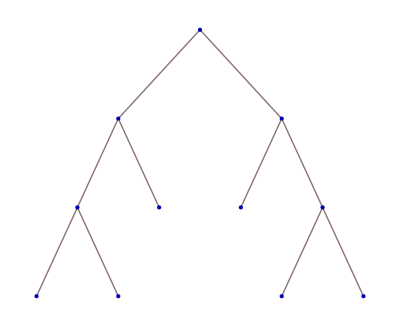
### binary trees avoiding -Graphics- (A159769)

```mathematica
Series[(-1+2 x-2 x^2+√(1-4 x+4 x^3))/(2 (-2 x^2+x^3)),{x,0,10}]
```

1+x+2 x^2+5 x^3+14 x^4+41 x^5+124 x^6+384 x^7+1212 x^8+3885 x^9+12614 x^10+O[x]^11

```mathematica
-1+x+(1-2 x+2 x^2) y+(-2+x) x^2 y^2/.y->y+1
```

-1+x+(1-2 x+2 x^2) (1+y)+(-2+x) x^2 (1+y)^2

```mathematica
Column[AbsoluteTiming[Grid[Function[modulus,{modulus,MissingResidues[AutomaticSequenceReduce[Mod[AlgebraicSequence[Function[y,-1+x+(1-2 x+2 x^2) (1+y)+(-2+x) x^2 (1+y)^2],x][n],modulus],n,Method->"Diagonal",Minimize->False,Monitor->True],modulus]}]/@(2^Range[5])]]]
```

32.0741
2 | {}
4 | {3}
8 | {3,7}
16 | {3,7,11,15}
32 | {3,7,11,15,19,23,25,27,29,31}

```mathematica
Select[{3,7,11,15,19,23,25,27,29,31},Mod[#,4]≠3&]
```

{25,29}

```mathematica
AbsoluteTiming[With[{modulus=64},MissingResidues[AutomaticSequenceReduce[Mod[AlgebraicSequence[Function[y,-1+x+(1-2 x+2 x^2) (1+y)+(-2+x) x^2 (1+y)^2],x][n],modulus],n,Method->"Diagonal",Minimize->False,Monitor->True],modulus]]]
```

{410.432,{3,7,9,11,13,15,19,22,23,25,27,29,31,35,37,39,43,47,51,55,57,59,61,63}}

```mathematica
Select[{3,7,9,11,13,15,19,22,23,25,27,29,31,35,37,39,43,47,51,55,57,59,61,63},!MatchQ[Mod[#,4],3]&&!MatchQ[Mod[#,32],25|29]&]
```

{9,13,22,37}

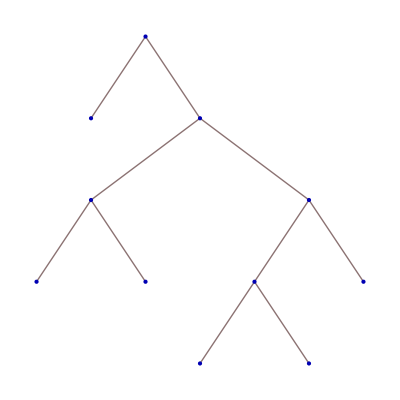
### binary trees avoiding -Graphics- (A159771)

```mathematica
Series[(1-2 x+3 x^2-√(1-4 x+2 x^2-4 x^3+x^4))/(4 x^2),{x,0,10}]
```

1+x+2 x^2+5 x^3+14 x^4+41 x^5+124 x^6+385 x^7+1220 x^8+3929 x^9+12822 x^10+O[x]^11

```mathematica
1-x+x^2+(-1+2 x-3 x^2) y+2 x^2 y^2/.y->y+1
```

1-x+x^2+(-1+2 x-3 x^2) (1+y)+2 x^2 (1+y)^2

```mathematica
Column[AbsoluteTiming[Grid[Function[modulus,{modulus,MissingResidues[AutomaticSequenceReduce[Mod[AlgebraicSequence[Function[y,1-x+x^2+(-1+2 x-3 x^2) (1+y)+2 x^2 (1+y)^2],x][n],modulus],n,Method->"Diagonal",Minimize->False],modulus]}]/@(2^Range[5])]]]
```

1.76352
2 | {}
4 | {3}
8 | {3,7}
16 | {3,7,11,13,15}
32 | {3,7,11,13,15,19,21,23,27,29,31}

```mathematica
AbsoluteTiming[With[{modulus=2^6},MissingResidues[AutomaticSequenceReduce[Mod[AlgebraicSequence[Function[y,1-x+x^2+(-1+2 x-3 x^2) (1+y)+2 x^2 (1+y)^2],x][n],modulus],n,Method->"Diagonal",Minimize->False,Monitor->True],modulus]]]
```

{22.236,{3,7,11,13,15,19,21,23,27,29,31,35,37,39,43,45,47,51,53,55,59,61,63}}

```mathematica
AbsoluteTiming[With[{modulus=2^7},MissingResidues[AutomaticSequenceReduce[Mod[AlgebraicSequence[Function[y,1-x+x^2+(-1+2 x-3 x^2) (1+y)+2 x^2 (1+y)^2],x][n],modulus],n,Method->"Diagonal",Minimize->False,Monitor->True],modulus]]]
```

{308.647,{3,7,11,13,15,19,21,23,27,29,31,35,37,39,43,45,47,51,53,55,59,61,63,67,71,75,77,79,83,85,87,91,93,95,99,101,103,107,109,111,115,117,119,123,125,127}}

```mathematica
Select[{3,7,11,13,15},Mod[#,4]≠3&]
```

{13}

```mathematica
Select[{3,7,11,13,15,19,21,23,27,29,31},Mod[#,4]≠3&&Mod[#,16]≠13&]
```

{21}

```mathematica
Select[{3,7,11,13,15,19,21,23,27,29,31,35,37,39,43,45,47,51,53,55,59,61,63},Mod[#,4]≠3&&Mod[#,16]≠13&&Mod[#,32]≠21&]
```

{37}

```mathematica
Select[{3,7,11,13,15,19,21,23,27,29,31,35,37,39,43,45,47,51,53,55,59,61,63,67,71,75,77,79,83,85,87,91,93,95,99,101,103,107,109,111,115,117,119,123,125,127},Mod[#,4]≠3&&Mod[#,16]≠13&&Mod[#,32]≠21&&Mod[#,64]≠37&]
```

{}

### permutations avoiding 3412 and 2143 (A029759)

```mathematica
Series[(1-3 x)/((1-2 x) √(1-4 x)),{x,0,10}]
```

1+x+2 x^2+6 x^3+22 x^4+86 x^5+340 x^6+1340 x^7+5254 x^8+20518 x^9+79932 x^10+O[x]^11

A polynomial of the correct form can be obtained by dropping the first two terms and dividing the remaining terms by 2:

```mathematica
Collect[((4 x-1) (2 x-1)^2 y^2+(3 x-1)^2/.y->1+x+2x y)/(4 x),y,Factor]
```

x (1-4 x+3 x^2+4 x^3)+(1+x) (-1+2 x)^2 (-1+4 x) y+x (-1+2 x)^2 (-1+4 x) y^2

```mathematica
Column[AbsoluteTiming[Grid[Function[modulus,{modulus,MissingResidues[AutomaticSequenceReduce[Mod[AlgebraicSequence[Function[y,x (1-4 x+3 x^2+4 x^3)+(1+x) (-1+2 x)^2 (-1+4 x) y+x (-1+2 x)^2 (-1+4 x) y^2],x][n],modulus],n,Method->"Diagonal",Minimize->False,Monitor->True],modulus]}]/@(2^Range[6])]]]
```

58.3136
2 | {}
4 | {}
8 | {5,7}
16 | {5,7,9,13,15}
32 | {5,7,9,13,15,17,21,23,25,27,29,31}
64 | {5,7,9,13,15,17,21,22,23,25,27,29,31,33,37,39,41,45,47,49,51,53,55,57,59,61,63}

```mathematica
Select[{5,7,9,13,15},!MemberQ[{5,7},Mod[#,8]]&]
```

{9}

```mathematica
Select[{5,7,9,13,15,17,21,23,25,27,29,31},!MemberQ[{5,7},Mod[#,8]]&&Mod[#,16]≠9&]
```

{17,27}

```mathematica
Select[{5,7,9,13,15,17,21,22,23,25,27,29,31,33,37,39,41,45,47,49,51,53,55,57,59,61,63},!MemberQ[{5,7},Mod[#,8]]&&Mod[#,16]≠9&&!MemberQ[{17,27},Mod[#,32]]&]
```

{22,33,51}

Multiply by 2:

```mathematica
2{5,7}
2{9}
2{17,27}
2{22,33,51}
```

{10,14}

{18}

{34,54}

{44,66,102}

### permutations avoiding 2143 and 1324 (A032351)

```mathematica
Series[(1-5 x+3 x^2+x^2 √(1-4 x))/(1-6 x+8 x^2-4 x^3),{x,0,10}]
```

1+x+2 x^2+6 x^3+22 x^4+88 x^5+366 x^6+1552 x^7+6652 x^8+28696 x^9+124310 x^10+O[x]^11

A polynomial of the correct form can be obtained by dropping the first three terms and dividing the remaining terms by 2:

```mathematica
Collect[(-1+4 x+x^2+2 (1-5 x+3 x^2) y+(-1+6 x-8 x^2+4 x^3) y^2/.y->1+x+2 x^2+2 x^2 y)/(4 x^4),y,Factor]
```

x (3-4 x+4 x^2)+(-1+8 x-12 x^2+8 x^3) y+(-1+6 x-8 x^2+4 x^3) y^2

```mathematica
Column[AbsoluteTiming[Grid[Function[modulus,{modulus,MissingResidues[AutomaticSequenceReduce[Mod[AlgebraicSequence[Function[y,x (3-4 x+4 x^2)+(-1+8 x-12 x^2+8 x^3) y+(-1+6 x-8 x^2+4 x^3) y^2],x][n],modulus],n,Method->"Diagonal",Minimize->False,Monitor->True],modulus]}]/@(2^Range[7])]]]
```

75.5017
2 | {}
4 | {1}
8 | {1,5}
16 | {1,5,9,13,15}
32 | {1,5,7,9,13,15,17,21,22,25,27,29,31}
64 | {1,5,7,9,13,15,17,19,21,22,23,25,27,29,30,31,33,37,38,39,41,43,45,47,49,53,54,57,59,61,63}
128 | {1,5,7,9,13,15,17,19,21,22,23,25,27,29,30,31,33,37,38,39,41,43,45,46,47,49,53,54,57,59,61,62,63,65,69,70,71,73,77,79,81,83,85,86,87,89,91,93,94,95,97,101,102,103,105,107,109,111,113,115,117,118,119,121,123,125,127}

```mathematica
Select[{1,5},Mod[#,4]≠1&]
```

{}

```mathematica
Select[{1,5,9,13,15},Mod[#,4]≠1&]
```

{15}

```mathematica
Select[{1,5,7,9,13,15,17,21,22,25,27,29,31},Mod[#,4]≠1&&Mod[#,16]≠15&]
```

{7,22,27}

```mathematica
Select[{1,5,7,9,13,15,17,19,21,22,23,25,27,29,30,31,33,37,38,39,41,43,45,47,49,53,54,57,59,61,63},Mod[#,4]≠1&&Mod[#,16]≠15&&!MemberQ[{7,22,27},Mod[#,32]]&]
```

{19,23,30,38,43}

```mathematica
Select[{1,5,7,9,13,15,17,19,21,22,23,25,27,29,30,31,33,37,38,39,41,43,45,46,47,49,53,54,57,59,61,62,63,65,69,70,71,73,77,79,81,83,85,86,87,89,91,93,94,95,97,101,102,103,105,107,109,111,113,115,117,118,119,121,123,125,127},Mod[#,4]≠1&&Mod[#,16]≠15&&!MemberQ[{7,22,27},Mod[#,32]]&&!MemberQ[{19,23,30,38,43},Mod[#,64]]&]
```

{46,62,70,115,119}

Multiply by 2:

```mathematica
2{1}
2{}
2{15}
2{7,22,27}
2{19,23,30,38,43}
2{46,62,70,115,119}
```

{2}

{}

{30}

{14,44,54}

{38,46,60,76,86}

{92,124,140,230,238}

### permutations avoiding 1342 and 2143 (A109033)

```mathematica
Series[(1-√(1-8 x+16 x^2-8 x^3))/(4 x (1-x)),{x,0,10}]
```

1+x+2 x^2+6 x^3+22 x^4+88 x^5+368 x^6+1584 x^7+6968 x^8+31192 x^9+141656 x^10+O[x]^11

```mathematica
Collect[((4 x (1-x) y-1)^2-(1-8 x+16 x^2-8 x^3))/(8 (-1+x) x),y,Factor]
%/.y->y+1
```

-1+x+y+2 (-1+x) x y^2

x+y+2 (-1+x) x (1+y)^2

```mathematica
Column[AbsoluteTiming[Grid[Function[modulus,{modulus,MissingResidues[AutomaticSequenceReduce[Mod[AlgebraicSequence[Function[y,x+y+2 (-1+x) x (1+y)^2],x][n],modulus],n,Method->"Diagonal",Minimize->False],modulus]}]/@(2^Range[10])]]]
```

4.37296
2 | {}
4 | {3}
8 | {3,4,5,7}
16 | {3,4,5,7,9,10,11,12,13,14,15}
32 | {3,4,5,7,8,9,10,11,12,13,14,15,17,18,19,20,21,23,25,26,27,28,29,30,31}
64 | {3,4,5,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,23,25,26,27,28,29,30,31,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,49,50,51,52,53,54,55,57,58,59,60,61,62,63}
128 | {3,4,5,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,49,50,51,52,53,54,55,57,58,59,60,61,62,63,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,89,90,91,92,93,94,95,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127}
256 | {3,4,5,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,49,50,51,52,53,54,55,57,58,59,60,61,62,63,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,217,218,219,220,221,222,223,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255}
512 | {3,4,5,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255,256,257,258,259,260,261,262,263,264,265,266,267,268,269,270,271,272,273,274,275,276,277,278,279,280,281,282,283,284,285,286,287,288,289,290,291,292,293,294,295,296,297,298,299,300,301,302,303,304,305,306,307,308,309,310,311,313,314,315,316,317,318,319,320,321,322,323,324,325,326,327,328,329,330,331,332,333,334,335,336,337,338,339,340,341,342,343,345,346,347,348,349,350,351,352,353,354,355,356,357,358,359,360,361,362,363,364,365,366,367,369,370,371,372,373,374,375,376,377,378,379,380,381,382,383,385,386,387,388,389,390,391,392,393,394,395,396,397,398,399,400,401,402,403,404,405,406,407,408,409,410,411,412,413,414,415,416,417,418,419,420,421,422,423,424,425,426,427,428,429,430,431,432,433,434,435,436,437,438,439,440,441,442,443,444,445,446,447,448,449,450,451,452,453,454,455,456,457,458,459,460,461,462,463,464,465,466,467,468,469,470,471,473,474,475,476,477,478,479,481,482,483,484,485,486,487,488,489,490,491,492,493,494,495,496,497,498,499,500,501,502,503,504,505,506,507,508,509,510,511}
1024 | {3,4,5,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255,256,257,258,259,260,261,262,263,264,265,266,267,268,269,270,271,272,273,274,275,276,277,278,279,280,281,282,283,284,285,286,287,288,289,290,291,292,293,294,295,296,297,298,299,300,301,302,303,304,305,306,307,308,309,310,311,312,313,314,315,316,317,318,319,320,321,322,323,324,325,326,327,328,329,330,331,332,333,334,335,336,337,338,339,340,341,342,343,345,346,347,348,349,350,351,352,353,354,355,356,357,358,359,360,361,362,363,364,365,366,367,369,370,371,372,373,374,375,376,377,378,379,380,381,382,383,385,386,387,388,389,390,391,392,393,394,395,396,397,398,399,400,401,402,403,404,405,406,407,408,409,410,411,412,413,414,415,416,417,418,419,420,421,422,423,424,425,426,427,428,429,430,431,432,433,434,435,436,437,438,439,440,441,442,443,444,445,446,447,448,449,450,451,452,453,454,455,456,457,458,459,460,461,462,463,464,465,466,467,468,469,470,471,473,474,475,476,477,478,479,481,482,483,484,485,486,487,488,489,490,491,492,493,494,495,496,497,498,499,500,501,502,503,504,505,506,507,508,509,510,511,513,514,515,516,517,518,519,520,521,522,523,524,525,526,527,528,529,530,531,532,533,534,535,536,537,538,539,540,541,542,543,544,545,546,547,548,549,550,551,552,553,554,555,556,557,558,559,561,562,563,564,565,566,567,568,569,570,571,572,573,574,575,577,578,579,580,581,582,583,584,585,586,587,588,589,590,591,592,593,594,595,596,597,598,599,600,601,602,603,604,605,606,607,608,609,610,611,612,613,614,615,616,617,618,619,620,621,622,623,624,625,626,627,628,629,630,631,632,633,634,635,636,637,638,639,640,641,642,643,644,645,646,647,648,649,650,651,652,653,654,655,656,657,658,659,660,661,662,663,664,665,666,667,668,669,670,671,672,673,674,675,676,677,678,679,680,681,682,683,684,685,686,687,688,689,690,691,692,693,694,695,696,697,698,699,700,701,702,703,705,706,707,708,709,710,711,712,713,714,715,716,717,718,719,720,721,722,723,724,725,726,727,728,729,730,731,732,733,734,735,736,737,738,739,740,741,742,743,744,745,746,747,748,749,750,751,752,753,754,755,756,757,758,759,760,761,762,763,764,765,766,767,768,769,770,771,772,773,774,775,776,777,778,779,780,781,782,783,784,785,786,787,788,789,790,791,792,793,794,795,796,797,798,799,800,801,802,803,804,805,806,807,808,809,810,811,812,813,814,815,816,817,818,819,820,821,822,823,825,826,827,828,829,830,831,832,833,834,835,836,837,838,839,840,841,842,843,844,845,846,847,848,849,850,851,852,853,854,855,856,857,858,859,860,861,862,863,864,865,866,867,868,869,870,871,872,873,874,875,876,877,878,879,880,881,882,883,884,885,886,887,888,889,890,891,892,893,894,895,897,898,899,900,901,902,903,904,905,906,907,908,909,910,911,912,913,914,915,916,917,918,919,920,921,922,923,924,925,926,927,928,929,930,931,932,933,934,935,936,937,938,939,940,941,942,943,944,945,946,947,948,949,950,951,952,953,954,955,956,957,958,959,960,961,962,963,964,965,966,967,968,969,970,971,972,973,974,975,976,977,978,979,980,981,982,983,984,985,986,987,988,989,990,991,993,994,995,996,997,998,999,1000,1001,1002,1003,1004,1005,1006,1007,1008,1009,1010,1011,1012,1013,1014,1015,1016,1017,1018,1019,1020,1021,1022,1023}

```mathematica
Select[{3,4,5,7},Mod[#,4]≠3&]
```

{4,5}

```mathematica
Select[{3,4,5,7,9,10,11,12,13,14,15},Mod[#,4]≠3&&!MemberQ[{4,5},Mod[#,8]]&]
```

{9,10,14}

```mathematica
Select[{3,4,5,7,8,9,10,11,12,13,14,15,17,18,19,20,21,23,25,26,27,28,29,30,31},Mod[#,4]≠3&&!MemberQ[{4,5},Mod[#,8]]&&!MemberQ[{9,10,14},Mod[#,16]]&]
```

{8,17,18}

```mathematica
Select[{3,4,5,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,23,25,26,27,28,29,30,31,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,49,50,51,52,53,54,55,57,58,59,60,61,62,63},Mod[#,4]≠3&&!MemberQ[{4,5},Mod[#,8]]&&!MemberQ[{9,10,14},Mod[#,16]]&&!MemberQ[{8,17,18},Mod[#,32]]&]
```

{16,33,34,38,54}

```mathematica
Select[{3,4,5,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,49,50,51,52,53,54,55,57,58,59,60,61,62,63,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,89,90,91,92,93,94,95,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127},Mod[#,4]≠3&&!MemberQ[{4,5},Mod[#,8]]&&!MemberQ[{9,10,14},Mod[#,16]]&&!MemberQ[{8,17,18},Mod[#,32]]&&!MemberQ[{16,33,34,38,54},Mod[#,64]]&]
```

{24,32,65,66,70,86,120}

```mathematica
Select[{3,4,5,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,49,50,51,52,53,54,55,57,58,59,60,61,62,63,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,217,218,219,220,221,222,223,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255},Mod[#,4]≠3&&!MemberQ[{4,5},Mod[#,8]]&&!MemberQ[{9,10,14},Mod[#,16]]&&!MemberQ[{8,17,18},Mod[#,32]]&&!MemberQ[{16,33,34,38,54},Mod[#,64]]&&!MemberQ[{24,32,65,66,70,86,120},Mod[#,128]]&]
```

{96,129,130,134,150,176,184,240}

```mathematica
Select[{3,4,5,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255,256,257,258,259,260,261,262,263,264,265,266,267,268,269,270,271,272,273,274,275,276,277,278,279,280,281,282,283,284,285,286,287,288,289,290,291,292,293,294,295,296,297,298,299,300,301,302,303,304,305,306,307,308,309,310,311,313,314,315,316,317,318,319,320,321,322,323,324,325,326,327,328,329,330,331,332,333,334,335,336,337,338,339,340,341,342,343,345,346,347,348,349,350,351,352,353,354,355,356,357,358,359,360,361,362,363,364,365,366,367,369,370,371,372,373,374,375,376,377,378,379,380,381,382,383,385,386,387,388,389,390,391,392,393,394,395,396,397,398,399,400,401,402,403,404,405,406,407,408,409,410,411,412,413,414,415,416,417,418,419,420,421,422,423,424,425,426,427,428,429,430,431,432,433,434,435,436,437,438,439,440,441,442,443,444,445,446,447,448,449,450,451,452,453,454,455,456,457,458,459,460,461,462,463,464,465,466,467,468,469,470,471,473,474,475,476,477,478,479,481,482,483,484,485,486,487,488,489,490,491,492,493,494,495,496,497,498,499,500,501,502,503,504,505,506,507,508,509,510,511},Mod[#,4]≠3&&!MemberQ[{4,5},Mod[#,8]]&&!MemberQ[{9,10,14},Mod[#,16]]&&!MemberQ[{8,17,18},Mod[#,32]]&&!MemberQ[{16,33,34,38,54},Mod[#,64]]&&!MemberQ[{24,32,65,66,70,86,120},Mod[#,128]]&&!MemberQ[{96,129,130,134,150,176,184,240},Mod[#,256]]&]
```

{56,112,216,224,256,257,258,262,278,304,320,448}

```mathematica
Select[{3,4,5,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255,256,257,258,259,260,261,262,263,264,265,266,267,268,269,270,271,272,273,274,275,276,277,278,279,280,281,282,283,284,285,286,287,288,289,290,291,292,293,294,295,296,297,298,299,300,301,302,303,304,305,306,307,308,309,310,311,312,313,314,315,316,317,318,319,320,321,322,323,324,325,326,327,328,329,330,331,332,333,334,335,336,337,338,339,340,341,342,343,345,346,347,348,349,350,351,352,353,354,355,356,357,358,359,360,361,362,363,364,365,366,367,369,370,371,372,373,374,375,376,377,378,379,380,381,382,383,385,386,387,388,389,390,391,392,393,394,395,396,397,398,399,400,401,402,403,404,405,406,407,408,409,410,411,412,413,414,415,416,417,418,419,420,421,422,423,424,425,426,427,428,429,430,431,432,433,434,435,436,437,438,439,440,441,442,443,444,445,446,447,448,449,450,451,452,453,454,455,456,457,458,459,460,461,462,463,464,465,466,467,468,469,470,471,473,474,475,476,477,478,479,481,482,483,484,485,486,487,488,489,490,491,492,493,494,495,496,497,498,499,500,501,502,503,504,505,506,507,508,509,510,511,513,514,515,516,517,518,519,520,521,522,523,524,525,526,527,528,529,530,531,532,533,534,535,536,537,538,539,540,541,542,543,544,545,546,547,548,549,550,551,552,553,554,555,556,557,558,559,561,562,563,564,565,566,567,568,569,570,571,572,573,574,575,577,578,579,580,581,582,583,584,585,586,587,588,589,590,591,592,593,594,595,596,597,598,599,600,601,602,603,604,605,606,607,608,609,610,611,612,613,614,615,616,617,618,619,620,621,622,623,624,625,626,627,628,629,630,631,632,633,634,635,636,637,638,639,640,641,642,643,644,645,646,647,648,649,650,651,652,653,654,655,656,657,658,659,660,661,662,663,664,665,666,667,668,669,670,671,672,673,674,675,676,677,678,679,680,681,682,683,684,685,686,687,688,689,690,691,692,693,694,695,696,697,698,699,700,701,702,703,705,706,707,708,709,710,711,712,713,714,715,716,717,718,719,720,721,722,723,724,725,726,727,728,729,730,731,732,733,734,735,736,737,738,739,740,741,742,743,744,745,746,747,748,749,750,751,752,753,754,755,756,757,758,759,760,761,762,763,764,765,766,767,768,769,770,771,772,773,774,775,776,777,778,779,780,781,782,783,784,785,786,787,788,789,790,791,792,793,794,795,796,797,798,799,800,801,802,803,804,805,806,807,808,809,810,811,812,813,814,815,816,817,818,819,820,821,822,823,825,826,827,828,829,830,831,832,833,834,835,836,837,838,839,840,841,842,843,844,845,846,847,848,849,850,851,852,853,854,855,856,857,858,859,860,861,862,863,864,865,866,867,868,869,870,871,872,873,874,875,876,877,878,879,880,881,882,883,884,885,886,887,888,889,890,891,892,893,894,895,897,898,899,900,901,902,903,904,905,906,907,908,909,910,911,912,913,914,915,916,917,918,919,920,921,922,923,924,925,926,927,928,929,930,931,932,933,934,935,936,937,938,939,940,941,942,943,944,945,946,947,948,949,950,951,952,953,954,955,956,957,958,959,960,961,962,963,964,965,966,967,968,969,970,971,972,973,974,975,976,977,978,979,980,981,982,983,984,985,986,987,988,989,990,991,993,994,995,996,997,998,999,1000,1001,1002,1003,1004,1005,1006,1007,1008,1009,1010,1011,1012,1013,1014,1015,1016,1017,1018,1019,1020,1021,1022,1023},Mod[#,4]≠3&&!MemberQ[{4,5},Mod[#,8]]&&!MemberQ[{9,10,14},Mod[#,16]]&&!MemberQ[{8,17,18},Mod[#,32]]&&!MemberQ[{16,33,34,38,54},Mod[#,64]]&&!MemberQ[{24,32,65,66,70,86,120},Mod[#,128]]&&!MemberQ[{96,129,130,134,150,176,184,240},Mod[#,256]]&&!MemberQ[{56,112,216,224,256,257,258,262,278,304,320,448},Mod[#,512]]&]
```

{48,192,312,513,514,518,534,600,640,856,880,984}

```mathematica
{8,17,18}-2^4
{16,33,34,38,54}-2^5
{24,32,65,66,70,86,120}-2^6
{96,129,130,134,150,176,184,240}-2^7
{56,112,216,224,256,257,258,262,278,304,320,448}-2^8
{48,192,312,513,514,518,534,600,640,856,880,984}-2^9
```

{-8,1,2}

{-16,1,2,6,22}

{-40,-32,1,2,6,22,56}

{-32,1,2,6,22,48,56,112}

{-200,-144,-40,-32,0,1,2,6,22,48,64,192}

{-464,-320,-200,1,2,6,22,88,128,344,368,472}

```mathematica
Grid[Table[{{2^(α-1)+1,2^(α-1)+2,2^(α-1)+6,2^(α-1)+22},2^α},{α,6,12}]]
```

{33,34,38,54} | 64
{65,66,70,86} | 128
{129,130,134,150} | 256
{257,258,262,278} | 512
{513,514,518,534} | 1024
{1025,1026,1030,1046} | 2048
{2049,2050,2054,2070} | 4096

## Computing automata for diagonals of rational functions modulo p^α

### Apéry numbers (A005259)

```mathematica
Table[AperyNumber[n],{n,0,10}]
```

{1,5,73,1445,33001,819005,21460825,584307365,16367912425,468690849005,13657436403073}

```mathematica
Table[DiagonalSequence[1/((1-x1-x2) (1-x3-x4)-x1 x2 x3 x4),{x1,x2,x3,x4}][n],{n,0,10}]
```

{1,5,73,1445,33001,819005,21460825,584307365,16367912425,468690849005,13657436403073}

#### 2^α

```mathematica
AutomaticSequenceAutomaton[AutomaticSequenceReduce[Mod[AperyNumber[n],2],n,Method->"Diagonal"]]
AutomatonGraph[%]
```

Automaton[{{1→1,0},{1→1,1}},1,{1→1},InputAlphabet→{0,1}]

-Graphics-

```mathematica
AutomaticSequenceAutomaton[AutomaticSequenceReduce[Mod[AperyNumber[n],2^2],n,Method->"Diagonal"]]
AutomatonGraph[%]
```

Automaton[{{1→1,0},{1→1,1}},1,{1→1},InputAlphabet→{0,1}]

-Graphics-

```mathematica
AutomaticSequenceAutomaton[AutomaticSequenceReduce[Mod[AperyNumber[n],2^3],n,Method->"Diagonal"]]
AutomatonGraph[%]
```

Automaton[{{1→2,0},{1→3,1},{2→2,0},{2→2,1},{3→3,0},{3→3,1}},1,{1→1,2→1,3→5},InputAlphabet→{0,1}]

-Graphics-

```mathematica
AutomaticSequenceAutomaton[AutomaticSequenceReduce[Mod[AperyNumber[n],2^4],n,Method->{"Diagonal","Degree"->"High"}]]
AutomatonGraph[%,VertexSize->.4]
```

Automaton[{{1→2,0},{1→3,1},{2→2,0},{2→4,1},{5→2,0},{5→5,1},{3→6,0},{3→3,1},{6→6,0},{6→7,1},{4→8,0},{4→4,1},{8→8,0},{8→5,1},{7→9,0},{7→7,1},{9→9,0},{9→3,1}},1,{1→1,2→1,3→5,4→9,5→1,6→5,7→13,8→9,9→13},InputAlphabet→{0,1}]

-Graphics-

```mathematica
AbsoluteTiming[AutomaticSequenceAutomaton[AutomaticSequenceReduce[Mod[AperyNumber[n],2^5],n,Method->{"Diagonal","Degree"->"High"},Monitor->True]]]
AutomatonGraph[%⟦2⟧,ImageSize->1000,VertexSize->.8]
```

{268.713,Automaton[{{1→2,0},{1→3,1},{2→2,0},{2→4,1},{5→6,0},{5→7,1},{6→2,0},{6→8,1},{9→6,0},{9→9,1},{3→10,0},{3→3,1},{10→11,0},{10→12,1},{11→11,0},{11→13,1},{14→10,0},{14→15,1},{4→16,0},{4→17,1},{16→18,0},{16→5,1},{18→18,0},{18→19,1},{20→16,0},{20→20,1},{17→21,0},{17→17,1},{21→22,0},{21→19,1},{22→22,0},{22→5,1},{8→21,0},{8→20,1},{12→23,0},{12→24,1},{23→25,0},{23→26,1},{27→23,0},{27→27,1},{25→25,0},{25→14,1},{13→28,0},{13→27,1},{24→28,0},{24→24,1},{28→29,0},{28→14,1},{29→29,0},{29→26,1},{19→30,0},{19→9,1},{7→30,0},{7→7,1},{30→31,0},{30→4,1},{31→31,0},{31→8,1},{26→32,0},{26→3,1},{32→33,0},{32→13,1},{15→32,0},{15→15,1},{33→33,0},{33→12,1}},1,{1→1,2→1,3→5,4→9,5→1,6→1,7→17,8→25,9→1,10→5,11→5,12→29,13→13,14→5,15→21,16→9,17→25,18→9,19→17,20→9,21→25,22→25,23→29,24→13,25→29,26→21,27→29,28→13,29→13,30→17,31→17,32→21,33→21},InputAlphabet→{0,1}]}

-Graphics-

#### 3^α

```mathematica
AutomaticSequenceAutomaton[AutomaticSequenceReduce[Mod[AperyNumber[n],3],n,Method->"Diagonal"]]
AutomatonGraph[%]
```

Automaton[{{1→1,0},{1→2,1},{1→1,2},{2→2,0},{2→1,1},{2→2,2}},1,{1→1,2→2},InputAlphabet→{0,1,2}]

-Graphics-

```mathematica
AutomaticSequenceAutomaton[AutomaticSequenceReduce[Mod[AperyNumber[n],3^2],n,Method->"Diagonal"]]
AutomatonGraph[%,GraphLayout->"SpringEmbedding"]
```

Automaton[{{1→1,0},{1→2,1},{1→1,2},{2→2,0},{2→3,1},{2→2,2},{3→3,0},{3→4,1},{3→3,2},{4→4,0},{4→5,1},{4→4,2},{5→5,0},{5→6,1},{5→5,2},{6→6,0},{6→1,1},{6→6,2}},1,{1→1,2→5,3→7,4→8,5→4,6→2},InputAlphabet→{0,1,2}]

-Graphics-

#### 5^α

There are many rational expressions for which the sequence of Apéry numbers is the diagonal:

```mathematica
Table[DiagonalSequence[1/((1-x1) ((1-x2) (1-x3) (1-x4) (1-x5)-x1 x2 x3)),{x1,x2,x3,x4,x5}][n],{n,0,5}]
```

{1,5,73,1445,33001,819005}

```mathematica
Table[DiagonalSequence[1/((1-x1 x2) (1-x3-x4-x1 x3 x4) (1-x5-x6-x2 x5 x6)),{x1,x2,x3,x4,x5,x6}][n],{n,0,5}]
```

{1,5,73,1445,33001,819005}

```mathematica
Table[DiagonalSequence[1/((1-x1-x2) (1-x3-x4)-x1 x2 x3 x4),{x1,x2,x3,x4}][n],{n,0,5}]
```

{1,5,73,1445,33001,819005}

For automaton computations, it can be advantageous to choose the expression that minimizes the number of monomials in denominator^((p-1)p^(α-1)):

```mathematica
AbsoluteTiming[With[{denominator=(1-x1) ((1-x2) (1-x3) (1-x4) (1-x5)-x1 x2 x3),modulus=5^2,p=5},Length[Expand[denominator^(modulus-modulus/p),Modulus->modulus]]]]
```

{1.3245,1285711}

```mathematica
AbsoluteTiming[With[{denominator=(1-x1 x2) (1-x3-x4-x1 x3 x4) (1-x5-x6-x2 x5 x6),modulus=5^2,p=5},Length[Expand[denominator^(modulus-modulus/p),Modulus->modulus]]]]
```

{0.276883,367837}

```mathematica
AbsoluteTiming[With[{denominator=(1-x1-x2) (1-x3-x4)-x1 x2 x3 x4,modulus=5^2,p=5},Length[Expand[denominator^(modulus-modulus/p),Modulus->modulus]]]]
```

{0.062909,49897}

By default, AutomaticSequenceReduce uses the preceding rational expression in four variables, which was discovered by Armin Straub.

```mathematica
AutomaticSequenceAutomaton[AutomaticSequenceReduce[Mod[AperyNumber[n],5],n,Method->"Diagonal"]]
AutomatonGraph[%,GraphLayout->"SpringEmbedding"]
```

Automaton[{{1→1,0},{1→2,1},{1→3,2},{1→2,3},{1→1,4},{2→2,0},{2→2,1},{2→2,2},{2→2,3},{2→2,4},{3→3,0},{3→2,1},{3→4,2},{3→2,3},{3→3,4},{4→4,0},{4→2,1},{4→5,2},{4→2,3},{4→4,4},{5→5,0},{5→2,1},{5→1,2},{5→2,3},{5→5,4}},1,{1→1,2→0,3→3,4→4,5→2},InputAlphabet→{0,1,2,3,4}]

-Graphics-

```mathematica
AbsoluteTiming[automaton25=AutomaticSequenceAutomaton[AutomaticSequenceReduce[Mod[AperyNumber[n],5^2],n,Method->"Diagonal",Minimize->False,Monitor->True]]]
```

{4.77836,Automaton[{{1→1,0},{1→2,1},{1→3,2},{1→4,3},{1→1,4},{2→5,0},{2→6,1},{2→6,2},{2→6,3},{2→7,4},{3→3,0},{3→8,1},{3→9,2},{3→10,3},{3→3,4},{4→7,0},{4→6,1},{4→6,2},{4→6,3},{4→5,4},{5→5,0},{5→6,1},{5→11,2},{5→6,3},{5→5,4},{6→6,0},{6→6,1},{6→6,2},{6→6,3},{6→6,4},{7→7,0},{7→6,1},{7→12,2},{7→6,3},{7→7,4},{8→11,0},{8→6,1},{8→6,2},{8→6,3},{8→12,4},{9→9,0},{9→4,1},{9→13,2},{9→2,3},{9→9,4},{10→12,0},{10→6,1},{10→6,2},{10→6,3},{10→11,4},{11→11,0},{11→6,1},{11→7,2},{11→6,3},{11→11,4},{12→12,0},{12→6,1},{12→5,2},{12→6,3},{12→12,4},{13→13,0},{13→10,1},{13→14,2},{13→8,3},{13→13,4},{14→14,0},{14→2,1},{14→15,2},{14→4,3},{14→14,4},{15→15,0},{15→8,1},{15→16,2},{15→10,3},{15→15,4},{16→16,0},{16→4,1},{16→17,2},{16→2,3},{16→16,4},{17→17,0},{17→10,1},{17→18,2},{17→8,3},{17→17,4},{18→18,0},{18→2,1},{18→19,2},{18→4,3},{18→18,4},{19→19,0},{19→8,1},{19→20,2},{19→10,3},{19→19,4},{20→20,0},{20→4,1},{20→21,2},{20→2,3},{20→20,4},{21→21,0},{21→10,1},{21→22,2},{21→8,3},{21→21,4},{22→22,0},{22→2,1},{22→23,2},{22→4,3},{22→22,4},{23→23,0},{23→8,1},{23→24,2},{23→10,3},{23→23,4},{24→24,0},{24→4,1},{24→25,2},{24→2,3},{24→24,4},{25→25,0},{25→10,1},{25→26,2},{25→8,3},{25→25,4},{26→26,0},{26→2,1},{26→27,2},{26→4,3},{26→26,4},{27→27,0},{27→8,1},{27→28,2},{27→10,3},{27→27,4},{28→28,0},{28→4,1},{28→29,2},{28→2,3},{28→28,4},{29→29,0},{29→10,1},{29→1,2},{29→8,3},{29→29,4}},1,{1→1,2→5,3→23,4→20,5→5,6→0,7→20,8→15,9→4,10→10,11→15,12→10,13→17,14→16,15→18,16→14,17→22,18→6,19→13,20→24,21→2,22→21,23→8,24→9,25→7,26→11,27→3,28→19,29→12}]}

```mathematica
AutomatonGraph[automaton25,ImageSize->700,VertexSize->1]
```

-Graphics-

After we see 1 or 3, we are in one of these five states:

```mathematica
Union[Cases[First[automaton25],{_->v_,1|3}:>v]]
```

{2,4,6,8,10}

There are some edges pointing from one of those five states to a state that is not in those five:

```mathematica
Cases[First[automaton25],{Alternatives@@{2,4,6,8,10}->Except[Alternatives@@{2,4,6,8,10}],_}]
```

{{2→5,0},{2→7,4},{4→7,0},{4→5,4},{8→11,0},{8→12,4},{10→12,0},{10→11,4}}

```mathematica
Union[Cases[First[automaton25],{Alternatives@@{2,4,6,8,10}->v:Except[Alternatives@@{2,4,6,8,10}],_}:>v]]
```

{5,7,11,12}

Whenever we see 1 or 3 from those states we go back to state 6, which outputs 0:

```mathematica
With[{externalstates=Union[Cases[First[automaton25],{Alternatives@@{2,4,6,8,10}->v:Except[Alternatives@@{2,4,6,8,10}],_}:>v]]},Cases[First[automaton25],{Alternatives@@externalstates->v_,1|3}:>v]]
```

{6,6,6,6,6,6,6,6}

And we don’t leave that set except to go to state 6:

```mathematica
Union[Cases[First[automaton25],{Alternatives@@{5,6,11,7,12}->v_,_}:>v]]
```

{5,6,7,11,12}

```mathematica
AutomatonGraph[Automaton[Cases[First[automaton25],{Alternatives@@{5,6,11,7,12}->_,_}],5]]
```

-Graphics-

In other words, only these vertices can be reached after seeing 1 or 3:

```mathematica
Union[{2,4,6,8,10},{5,6,11,7,12}]
```

{2,4,5,6,7,8,10,11,12}

And all the edges labeled 1 or 3 leaving one of those nine vertices point to vertex 6:

```mathematica
Cases[First[automaton25],{Alternatives@@{2,4,6,8,10,5,7,11,12}->v_,1|3}:>v]
```

{6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6}

So Beuker’s conjecture holds for α==2.

Delete vertices that correspond to outputs divisible by 5:

```mathematica
With[{graph=AutomatonGraph[automaton25,GraphLayout->"SpringEmbedding",VertexSize->.35]},VertexDelete[graph,Cases[VertexList[graph],Interpretation[label_/;Divisible[label,5],_]]]]
```

-Graphics-

```mathematica
Mod[23^Range[0,20],25]
```

{1,23,4,17,16,18,14,22,6,13,24,2,21,8,9,7,11,3,19,12,1}

```mathematica
Clear[automaton25]
```

#### 7^α

```mathematica
AutomaticSequenceAutomaton[AutomaticSequenceReduce[Mod[AperyNumber[n],7],n,Method->"Diagonal"]]
AutomatonGraph[%,GraphLayout->"SpringEmbedding"]
```

Automaton[{{1→1,0},{1→2,1},{1→3,2},{1→3,3},{1→3,4},{1→2,5},{1→1,6},{2→2,0},{2→4,1},{2→1,2},{2→1,3},{2→1,4},{2→4,5},{2→2,6},{3→3,0},{3→1,1},{3→5,2},{3→5,3},{3→5,4},{3→1,5},{3→3,6},{4→4,0},{4→6,1},{4→2,2},{4→2,3},{4→2,4},{4→6,5},{4→4,6},{5→5,0},{5→3,1},{5→6,2},{5→6,3},{5→6,4},{5→3,5},{5→5,6},{6→6,0},{6→5,1},{6→4,2},{6→4,3},{6→4,4},{6→5,5},{6→6,6}},1,{1→1,2→5,3→3,4→4,5→2,6→6},InputAlphabet→{0,1,2,3,4,5,6}]

-Graphics-

```mathematica
AbsoluteTiming[AutomaticSequenceAutomaton[AutomaticSequenceReduce[Mod[AperyNumber[n],7^2],n,Method->"Diagonal",Minimize->False,Monitor->True]]]
AutomatonGraph[%⟦2⟧,GraphLayout->"SpringEmbedding",ImageSize->1000,VertexSize->.7]
```

{229.011,Automaton[{{1→1,0},{1→2,1},{1→3,2},{1→3,3},{1→3,4},{1→4,5},{1→1,6},{2→5,0},{2→6,1},{2→7,2},{2→8,3},{2→1,4},{2→9,5},{2→10,6},{3→3,0},{3→11,1},{3→12,2},{3→12,3},{3→12,4},{3→13,5},{3→3,6},{4→10,0},{4→14,1},{4→1,2},{4→8,3},{4→7,4},{4→15,5},{4→5,6},{5→5,0},{5→16,1},{5→17,2},{5→17,3},{5→17,4},{5→18,5},{5→5,6},{6→19,0},{6→20,1},{6→10,2},{6→5,3},{6→21,4},{6→22,5},{6→23,6},{7→7,0},{7→24,1},{7→25,2},{7→25,3},{7→25,4},{7→26,5},{7→7,6},{8→8,0},{8→27,1},{8→28,2},{8→28,3},{8→28,4},{8→29,5},{8→8,6},{9→30,0},{9→31,1},{9→32,2},{9→33,3},{9→34,4},{9→22,5},{9→35,6},{10→10,0},{10→36,1},{10→37,2},{10→37,3},{10→37,4},{10→38,5},{10→10,6},{11→17,0},{11→39,1},{11→25,2},{11→28,3},{11→3,4},{11→40,5},{11→37,6},{12→12,0},{12→41,1},{12→42,2},{12→42,3},{12→42,4},{12→43,5},{12→12,6},{13→37,0},{13→44,1},{13→3,2},{13→28,3},{13→25,4},{13→45,5},{13→17,6},{14→35,0},{14→46,1},{14→34,2},{14→33,3},{14→32,4},{14→47,5},{14→30,6},{15→23,0},{15→46,1},{15→21,2},{15→5,3},{15→10,4},{15→48,5},{15→19,6},{16→23,0},{16→49,1},{16→32,2},{16→10,3},{16→5,4},{16→50,5},{16→51,6},{17→17,0},{17→52,1},{17→53,2},{17→53,3},{17→53,4},{17→54,5},{17→17,6},{18→51,0},{18→55,1},{18→5,2},{18→10,3},{18→32,4},{18→56,5},{18→23,6},{19→19,0},{19→49,1},{19→33,2},{19→33,3},{19→33,4},{19→56,5},{19→19,6},{20→57,0},{20→58,1},{20→23,2},{20→19,3},{20→59,4},{20→60,5},{20→61,6},{21→21,0},{21→6,1},{21→62,2},{21→62,3},{21→62,4},{21→15,5},{21→21,6},{22→63,0},{22→64,1},{22→51,2},{22→35,3},{22→30,4},{22→60,5},{22→65,6},{23→23,0},{23→66,1},{23→34,2},{23→34,3},{23→34,4},{23→67,5},{23→23,6},{24→32,0},{24→36,1},{24→17,2},{24→62,3},{24→7,4},{24→68,5},{24→33,6},{25→25,0},{25→69,1},{25→70,2},{25→70,3},{25→70,4},{25→71,5},{25→25,6},{26→33,0},{26→72,1},{26→7,2},{26→62,3},{26→17,4},{26→38,5},{26→32,6},{27→10,0},{27→16,1},{27→62,2},{27→7,3},{27→8,4},{27→73,5},{27→32,6},{28→28,0},{28→74,1},{28→75,2},{28→75,3},{28→75,4},{28→76,5},{28→28,6},{29→32,0},{29→77,1},{29→8,2},{29→7,3},{29→62,4},{29→18,5},{29→10,6},{30→30,0},{30→78,1},{30→5,2},{30→5,3},{30→5,4},{30→79,5},{30→30,6},{31→42,0},{31→64,1},{31→19,2},{31→59,3},{31→80,4},{31→81,5},{31→57,6},{32→32,0},{32→14,1},{32→82,2},{32→82,3},{32→82,4},{32→9,5},{32→32,6},{33→33,0},{33→77,1},{33→1,2},{33→1,3},{33→1,4},{33→73,5},{33→33,6},{34→34,0},{34→72,1},{34→8,2},{34→8,3},{34→8,4},{34→68,5},{34→34,6},{35→35,0},{35→55,1},{35→21,2},{35→21,3},{35→21,4},{35→50,5},{35→35,6},{36→51,0},{36→66,1},{36→33,2},{36→32,3},{36→10,4},{36→79,5},{36→35,6},{37→37,0},{37→83,1},{37→84,2},{37→84,3},{37→84,4},{37→85,5},{37→37,6},{38→35,0},{38→78,1},{38→10,2},{38→32,3},{38→33,4},{38→67,5},{38→51,6},{39→33,0},{39→14,1},{39→37,2},{39→17,3},{39→62,4},{39→86,5},{39→34,6},{40→5,0},{40→36,1},{40→82,2},{40→1,3},{40→8,4},{40→86,5},{40→21,6},{41→53,0},{41→87,1},{41→70,2},{41→75,3},{41→12,4},{41→88,5},{41→84,6},{42→42,0},{42→58,1},{42→51,2},{42→51,3},{42→51,4},{42→89,5},{42→42,6},{43→84,0},{43→90,1},{43→12,2},{43→75,3},{43→70,4},{43→91,5},{43→53,6},{44→21,0},{44→92,1},{44→8,2},{44→1,3},{44→82,4},{44→38,5},{44→5,6},{45→34,0},{45→92,1},{45→62,2},{45→17,3},{45→37,4},{45→9,5},{45→33,6},{46→65,0},{46→93,1},{46→30,2},{46→35,3},{46→51,4},{46→94,5},{46→63,6},{47→57,0},{47→95,1},{47→80,2},{47→59,3},{47→19,4},{47→94,5},{47→42,6},{48→61,0},{48→93,1},{48→59,2},{48→19,3},{48→23,4},{48→89,5},{48→57,6},{49→61,0},{49→96,1},{49→51,2},{49→23,3},{49→19,4},{49→97,5},{49→98,6},{50→99,0},{50→58,1},{50→35,2},{50→30,3},{50→80,4},{50→97,5},{50→63,6},{51→51,0},{51→46,1},{51→100,2},{51→100,3},{51→100,4},{51→22,5},{51→51,6},{52→34,0},{52→77,1},{52→82,2},{52→37,3},{52→17,4},{52→15,5},{52→100,6},{53→53,0},{53→101,1},{53→102,2},{53→102,3},{53→102,4},{53→103,5},{53→53,6},{54→100,0},{54→6,1},{54→17,2},{54→37,3},{54→82,4},{54→73,5},{54→34,6},{55→63,0},{55→104,1},{55→80,2},{55→30,3},{55→35,4},{55→89,5},{55→99,6},{56→98,0},{56→104,1},{56→19,2},{56→23,3},{56→51,4},{56→105,5},{56→61,6},{57→57,0},{57→96,1},{57→35,2},{57→35,3},{57→35,4},{57→105,5},{57→57,6},{58→102,0},{58→106,1},{58→61,2},{58→57,3},{58→42,4},{58→107,5},{58→108,6},{59→59,0},{59→20,1},{59→32,2},{59→32,3},{59→32,4},{59→48,5},{59→59,6},{60→75,0},{60→109,1},{60→98,2},{60→65,3},{60→63,4},{60→107,5},{60→12,6},{61→61,0},{61→95,1},{61→30,2},{61→30,3},{61→30,4},{61→81,5},{61→61,6},{62→62,0},{62→39,1},{62→110,2},{62→110,3},{62→110,4},{62→45,5},{62→62,6},{63→63,0},{63→111,1},{63→19,2},{63→19,3},{63→19,4},{63→112,5},{63→63,6},{64→113,0},{64→109,1},{64→57,2},{64→42,3},{64→99,4},{64→114,5},{64→102,6},{65→65,0},{65→104,1},{65→59,2},{65→59,3},{65→59,4},{65→97,5},{65→65,6},{66→98,0},{66→95,1},{66→35,2},{66→51,3},{66→23,4},{66→112,5},{66→65,6},{67→65,0},{67→111,1},{67→23,2},{67→51,3},{67→35,4},{67→81,5},{67→98,6},{68→59,0},{68→49,1},{68→34,2},{68→100,3},{68→21,4},{68→79,5},{68→80,6},{69→82,0},{69→83,1},{69→53,2},{69→110,3},{69→25,4},{69→29,5},{69→1,6},{70→70,0},{70→109,1},{70→61,2},{70→61,3},{70→61,4},{70→115,5},{70→70,6},{71→1,0},{71→27,1},{71→25,2},{71→110,3},{71→53,4},{71→85,5},{71→82,6},{72→80,0},{72→78,1},{72→21,2},{72→100,3},{72→34,4},{72→56,5},{72→59,6},{73→80,0},{73→20,1},{73→33,2},{73→34,3},{73→100,4},{73→50,5},{73→30,6},{74→37,0},{74→52,1},{74→110,2},{74→25,3},{74→28,4},{74→4,5},{74→82,6},{75→75,0},{75→116,1},{75→57,2},{75→57,3},{75→57,4},{75→117,5},{75→75,6},{76→82,0},{76→2,1},{76→28,2},{76→25,3},{76→110,4},{76→54,5},{76→37,6},{77→30,0},{77→55,1},{77→100,2},{77→34,3},{77→33,4},{77→48,5},{77→80,6},{78→99,0},{78→111,1},{78→59,2},{78→80,3},{78→30,4},{78→105,5},{78→42,6},{79→42,0},{79→96,1},{79→30,2},{79→80,3},{79→59,4},{79→112,5},{79→99,6},{80→80,0},{80→31,1},{80→10,2},{80→10,3},{80→10,4},{80→47,5},{80→80,6},{81→12,0},{81→116,1},{81→61,2},{81→98,3},{81→65,4},{81→114,5},{81→118,6},{82→82,0},{82→44,1},{82→119,2},{82→119,3},{82→119,4},{82→40,5},{82→82,6},{83→100,0},{83→72,1},{83→1,2},{83→82,3},{83→37,4},{83→18,5},{83→21,6},{84→84,0},{84→120,1},{84→108,2},{84→108,3},{84→108,4},{84→121,5},{84→84,6},{85→21,0},{85→16,1},{85→37,2},{85→82,3},{85→1,4},{85→68,5},{85→100,6},{86→19,0},{86→66,1},{86→100,2},{86→21,3},{86→5,4},{86→47,5},{86→59,6},{87→1,0},{87→44,1},{87→84,2},{87→53,3},{87→110,4},{87→26,5},{87→8,6},{88→17,0},{88→83,1},{88→119,2},{88→3,3},{88→28,4},{88→26,5},{88→62,6},{89→108,0},{89→122,1},{89→42,2},{89→57,3},{89→61,4},{89→123,5},{89→102,6},{90→62,0},{90→24,1},{90→28,2},{90→3,3},{90→119,4},{90→85,5},{90→17,6},{91→8,0},{91→24,1},{91→110,2},{91→53,3},{91→84,4},{91→40,5},{91→1,6},{92→59,0},{92→31,1},{92→5,2},{92→21,3},{92→100,4},{92→67,5},{92→19,6},{93→12,0},{93→122,1},{93→63,2},{93→65,3},{93→98,4},{93→115,5},{93→75,6},{94→102,0},{94→124,1},{94→99,2},{94→42,3},{94→57,4},{94→115,5},{94→113,6},{95→118,0},{95→124,1},{95→65,2},{95→98,3},{95→61,4},{95→117,5},{95→12,6},{96→108,0},{96→125,1},{96→98,2},{96→61,3},{96→57,4},{96→43,5},{96→118,6},{97→70,0},{97→106,1},{97→65,2},{97→63,3},{97→99,4},{97→43,5},{97→75,6},{98→98,0},{98→93,1},{98→80,2},{98→80,3},{98→80,4},{98→60,5},{98→98,6},{99→99,0},{99→64,1},{99→23,2},{99→23,3},{99→23,4},{99→94,5},{99→99,6},{100→100,0},{100→92,1},{100→7,2},{100→7,3},{100→7,4},{100→86,5},{100→100,6},{101→8,0},{101→2,1},{101→119,2},{101→84,3},{101→53,4},{101→45,5},{101→7,6},{102→102,0},{102→125,1},{102→65,2},{102→65,3},{102→65,4},{102→126,5},{102→102,6},{103→7,0},{103→39,1},{103→53,2},{103→84,3},{103→119,4},{103→4,5},{103→8,6},{104→75,0},{104→41,1},{104→99,2},{104→63,3},{104→65,4},{104→123,5},{104→70,6},{105→118,0},{105→41,1},{105→57,2},{105→61,3},{105→98,4},{105→126,5},{105→108,6},{106→3,0},{106→90,1},{106→108,2},{106→102,3},{106→113,4},{106→71,5},{106→28,6},{107→53,0},{107→120,1},{107→118,2},{107→12,3},{107→75,4},{107→71,5},{107→110,6},{108→108,0},{108→124,1},{108→63,2},{108→63,3},{108→63,4},{108→114,5},{108→108,6},{109→119,0},{109→120,1},{109→102,2},{109→113,3},{109→70,4},{109→76,5},{109→3,6},{110→110,0},{110→87,1},{110→113,2},{110→113,3},{110→113,4},{110→91,5},{110→110,6},{111→70,0},{111→116,1},{111→42,2},{111→99,3},{111→63,4},{111→126,5},{111→113,6},{112→113,0},{112→125,1},{112→63,2},{112→99,3},{112→42,4},{112→117,5},{112→70,6},{113→113,0},{113→106,1},{113→98,2},{113→98,3},{113→98,4},{113→123,5},{113→113,6},{114→110,0},{114→101,1},{114→108,2},{114→118,3},{114→12,4},{114→76,5},{114→25,6},{115→3,0},{115→74,1},{115→70,2},{115→113,3},{115→102,4},{115→121,5},{115→119,6},{116→84,0},{116→101,1},{116→113,2},{116→70,3},{116→75,4},{116→13,5},{116→119,6},{117→119,0},{117→11,1},{117→75,2},{117→70,3},{117→113,4},{117→103,5},{117→84,6},{118→118,0},{118→122,1},{118→99,2},{118→99,3},{118→99,4},{118→107,5},{118→118,6},{119→119,0},{119→90,1},{119→118,2},{119→118,3},{119→118,4},{119→88,5},{119→119,6},{120→7,0},{120→27,1},{120→3,2},{120→119,3},{120→84,4},{120→54,5},{120→62,6},{121→62,0},{121→52,1},{121→84,2},{121→119,3},{121→3,4},{121→29,5},{121→7,6},{122→110,0},{122→69,1},{122→75,2},{122→12,3},{122→118,4},{122→121,5},{122→53,6},{123→28,0},{123→69,1},{123→113,2},{123→102,3},{123→108,4},{123→88,5},{123→3,6},{124→25,0},{124→74,1},{124→12,2},{124→118,3},{124→108,4},{124→103,5},{124→110,6},{125→28,0},{125→11,1},{125→118,2},{125→108,3},{125→102,4},{125→91,5},{125→25,6},{126→25,0},{126→87,1},{126→102,2},{126→108,3},{126→118,4},{126→13,5},{126→28,6}},1,{1→1,2→5,3→24,4→19,5→5,6→4,7→36,8→43,9→39,10→19,11→22,12→37,13→15,14→18,15→25,16→25,17→22,18→46,19→4,20→13,21→40,22→41,23→25,24→33,25→31,26→47,27→19,28→3,29→33,30→39,31→6,32→33,33→47,34→12,35→18,36→46,37→15,38→18,39→47,40→5,41→38,42→6,43→17,44→40,45→12,46→34,47→13,48→20,49→20,50→48,51→46,52→12,53→38,54→26,55→41,56→27,57→13,58→30,59→32,60→23,61→20,62→29,63→41,64→44,65→34,66→27,67→34,68→32,69→8,70→9,71→1,72→11,73→11,74→15,75→23,76→8,77→39,78→48,79→6,80→11,81→37,82→8,83→26,84→17,85→40,86→4,87→1,88→22,89→16,90→29,91→43,92→32,93→37,94→30,95→2,96→16,97→9,98→27,99→48,100→26,101→43,102→30,103→36,104→23,105→2,106→24,107→38,108→16,109→45,110→10,111→9,112→44,113→44,114→10,115→24,116→17,117→45,118→2,119→45,120→36,121→29,122→10,123→3,124→31,125→3,126→31}]}

-Graphics-

### ζ(2) Apéry numbers (A005258)

```mathematica
Table[∑_(k=0)^n Binomial[n,k]^2 Binomial[n+k,k],{n,0,6}]
```

{1,3,19,147,1251,11253,104959}

```mathematica
Table[DiagonalSequence[1/((1-x1) (1-x2) (1-x3) (1-x4)-(1-x1) x1 x2 x3),{x1,x2,x3,x4}][n],{n,0,6}]
```

{1,3,19,147,1251,11253,104959}

```mathematica
AutomaticSequenceAutomaton[AutomaticSequenceReduce[Mod[DiagonalSequence[1/((1-x1) (1-x2) (1-x3) (1-x4)-(1-x1) x1 x2 x3),{x1,x2,x3,x4}][n],3^2],n,Minimize->False]]
AutomatonGraph[%,GraphLayout->"SpringEmbedding"]
```

Automaton[{{1→1,0},{1→2,1},{1→1,2},{2→3,0},{2→4,1},{2→5,2},{3→3,0},{3→4,1},{3→3,2},{4→4,0},{4→4,1},{4→4,2},{5→5,0},{5→4,1},{5→5,2}},1,{1→1,2→3,3→3,4→0,5→6}]

-Graphics-

## Computing automata for algebraic sequences by incrementally raising the exponent

### central trinomial coefficients (A002426)

The following is support code for the function AutomaticSequenceReduceList below, which computes automata for an algebraic sequence modulo p,p^2,…,p^α.
It is quite slow relative to AutomaticSequenceReduce, however.

```mathematica
ExtractFactor[polynomial_,y_,series_]:=
With[{factorlist=Select[First/@Rest[FactorList[polynomial]],Normal[#/.y->series]===0&]},
If[factorlist=={},
Print["no factors!"];$Failed
,
If[Length[factorlist]≥2,
Print["multiple factors! using last"]
];
SeriesRoot[{Function@@{Last[factorlist]/.y->#},series}]
]
]
```

```mathematica
SeriesRootPlus[SeriesRoot[{p_Function,f0_SeriesData}],SeriesRoot[{q_Function,g0_SeriesData}]]:=
Module[{factor,x,y},
factor=ExtractFactor[Resultant[p[x],q[y-x],x],y,f0+g0];
factor/;factor=!=$Failed
]
SeriesRootPlus[p_SeriesRoot,q_SeriesRoot,symbolicroots__SeriesRoot]:=
SeriesRootPlus[SeriesRootPlus[p,q],symbolicroots]
SeriesRootPlus[p_SeriesRoot]:=p
```

```mathematica
SeriesRootSubtract[SeriesRoot[{p_Function,f0_SeriesData}],SeriesRoot[{q_Function,g0_SeriesData}]]:=
Module[{factor,x,y},
factor=ExtractFactor[Resultant[p[x],q[x-y],x],y,f0-g0];
factor/;factor=!=$Failed
]
```

```mathematica
SeriesRootTimes[SeriesRoot[{p_Function,f0_SeriesData}],SeriesRoot[{q_Function,g0_SeriesData}]]:=
Module[{factor,x,y},
factor=ExtractFactor[Resultant[p[x],x^Exponent[q[x],x] q[y/x],x],y,f0 g0];
factor/;factor=!=$Failed
]
SeriesRootTimes[p_SeriesRoot,q_SeriesRoot,symbolicroots__SeriesRoot]:=
SeriesRootTimes[SeriesRootTimes[p,q],symbolicroots]
SeriesRootTimes[p_SeriesRoot]:=p
```

```mathematica
DilateSeries[series:HoldPattern[SeriesData][variable_,__],exponent_]:=(Normal[series]/.variable->variable^exponent)+O[variable]^(exponent series⟦5⟧)
```

```mathematica
DilateSeriesRoot[SeriesRoot[{f_Function,series:HoldPattern[SeriesData][x_,__]},options___],exponent_Integer?Positive]:=SeriesRoot[{f/.x->x^exponent,DilateSeries[series,exponent]},options]
```

```mathematica
AutomaticSequenceReduceList[Mod[AlgebraicSequence[seriesroot:SeriesRoot[{_Function,HoldPattern[SeriesData][x_,0,__]}]][n_],modulus_?PrimePowerQ],n_,OptionsPattern[]]:=
Module[{p,α,unprojectedcurrentcomponentseries,componentautomaton,christoloperator,coefficientrules,liftedseries,Deltaseries,y,δ,christoloutputseries,deltapolynomial,Deltapolynomial,seriesterms},
{p,α}=NumberTheory`PrimePower[modulus];
unprojectedcurrentcomponentseries=seriesroot;
componentautomaton[0]=AutomaticSequenceAutomaton[AutomaticSequenceReduce[Mod[AlgebraicSequence[seriesroot][n],p],n,Minimize->OptionValue[Minimize],Monitor->OptionValue[Monitor]]];
Do[
christoloperator=IntegerSequences`Private`ChristolPolynomial[componentautomaton[i-1],{x,δ},Modulus->0];
coefficientrules=CoefficientRules[christoloperator,δ];
Do[
(* With indices, liftedseries would be liftedseries[i-1,j-1], but we only need one at a time.
 liftedseries[i-1,j-1] is congruent modulo p^(i-1) to the lifting of the ith component. *)
liftedseries=If[j==2,
unprojectedcurrentcomponentseries,
(* Compute a polynomial for liftedseries[i-1,j-1]. *)
SeriesRootSubtract[If[i==1,seriesroot,SeriesRootPlus@@Table[Deltaseries[i-k,k],{k,2,i}]],Replace[SeriesRootPlus@@Table[SeriesRootTimes[SeriesRoot[{Function@@{y,y-p^(k-1)},p^(k-1)+O[x]^(Deltaseries[i-1,k]⟦1,2,5⟧)}],Deltaseries[i-1,k]],{k,2,j-1}],SeriesRootPlus[]->SeriesRoot[{#&,O[x]^100}]]]
];
(* Compute a polynomial for the Christol operator evaluated at liftedseries[i-1,j-1]. *)
christoloutputseries=SeriesRootPlus@@(SeriesRootTimes[SeriesRoot[{Function@@{y,y-#2},#2+O[x]^(#1⟦1⟧ liftedseries⟦1,2,5⟧)}],DilateSeriesRoot[liftedseries,#1⟦1⟧]]&@@@coefficientrules);
(* Into the polynomial we just computed, plug in the Christol polynomial (in δ) times p^(j-1). *)
deltapolynomial=christoloutputseries⟦1,1⟧[p^(j-1) christoloperator];
deltapolynomial=Cancel[deltapolynomial/(GCD@@Last/@CoefficientRules[deltapolynomial,{x,δ}])];
(* Compute an Ore polynomial for δ, and lift it to an algebraic Subscript[Δ, i-1]^j with integer coefficients. *)
Deltapolynomial=OrePolynomial[deltapolynomial,{x,δ},p,Modulus->p];
(* This test is not perfect because CoefficientList[O[x]^10,x] is the empty list, so there may be a problem for the zero sequence. *)
seriesterms=Select[δ[x]/.DeleteDuplicates[SeriesSolve[Deltapolynomial==0/.δ->δ[x],δ[x],{x,0,5}]],MatchQ[#,HoldPattern[SeriesData][_,_,{__Integer},__]]&];
Deltaseries[i-1,j]=SeriesRoot[{Function@@{δ,Deltapolynomial},First[seriesterms]}]
,
{j,2,α+1-i}
];
unprojectedcurrentcomponentseries=SeriesRootPlus@@Table[Deltaseries[i-j+1,j],{j,2,i+1}];
componentautomaton[i]=AutomaticSequenceAutomaton[AutomaticSequenceReduce[Mod[AlgebraicSequence[unprojectedcurrentcomponentseries][n],p],n,Minimize->OptionValue[Minimize],Monitor->OptionValue[Monitor]]]
,
{i,1,α-1}
];
Table[AutomaticSequence[componentautomaton[i]][n],{i,0,α-1}]
]
Options[AutomaticSequenceReduceList]={Minimize->True,Monitor->False};
```

```mathematica
Series[1/(√(1-2 x-3 x^2)),{x,0,10}]
```

1+x+3 x^2+7 x^3+19 x^4+51 x^5+141 x^6+393 x^7+1107 x^8+3139 x^9+8953 x^10+O[x]^11

```mathematica
AutomaticSequenceAutomaton/@AutomaticSequenceReduceList[Mod[AlgebraicSequence[SeriesRoot[{Function[y,(x+1) (3 x-1) y^2+1],Series[1/(√(1-2 x-3 x^2)),{x,0,15}]}]][n],2^2],n,Minimize->False]
AutomatonGraph/@%
```

{Automaton[{{1→1,0},{1→1,1}},1,{1→1}],Automaton[{{1→2,0},{1→2,1},{2→3,0},{2→4,1},{3→2,0},{3→5,1},{4→5,0},{4→2,1},{5→4,0},{5→3,1}},1,{1→0,2→0,3→0,4→1,5→1}]}

{-Graphics-,-Graphics-}